```mathematica
SetDirectory[NotebookDirectory[]];
Import["FunctionsAndConstants.wl"] ;(* parents directory could be "../LLR/FunctionsAndConstants.wl" etc*)
Needs["NDSolve`FEM`"];
Needs["NumericalCalculus`"];
Needs["MaTeX`"]
flim=Import["cannex_sensitivity_curves.csv"][[1;;]];
PressSen=Interpolation[flim[[All,1;;2]]]; (*Function of d in meters, output in N/m^2*)
PressGradSen=Interpolation[flim[[All,1;;3;;2]]]; (*Function of d in meters, output in N/m^3*)

Veff[Λ_,Mc_,n_,ρ_,ϕ_]:=(ρ ϕ)/Mc+Λ^(4+n) ϕ^-n
ϕρ[Λ_,Mc_,n_,ρ_]:=(SetPrecision[(n*Mc* Λ^(4+n))/ρ,1000])^(1/(n+1))
μ[Λ_,n_,Mc_,ρ_]:=√(((n+1) n Λ^(4+n))/ϕρ[Λ,Mc,n,ρ]^(n+2))
mm=SetPrecision[0.001*m2invMeV,1000];(*1mm in MeV*)
```

## Deriving two mirror solution

In this section I completely derive the two mirror solution for n=1, following the steps in the paper. The goal is to have a completely error free final implementation.  There is an error in the paper and some functions are defined differently in mathematica as suggested in the paper, which is why I will check every step thouroughly will double check the derivation in terms of mathematica functions.

```mathematica
Clear[Veff,RHS,LHS,ϕρ]
Veff[Λ_,β_,ρ_,ϕ_]:=Λ^5/ϕ+β*ρ/mpl ϕ
ϕρ[Λ_,β_,ρ_]:=√((Λ^5 mpl)/(β ρ))
(*I start with the DGL in integrated form, this is equation (3) in the paper*)
LHS[z_]=1/2 ϕ'[z]^2; (*LHS of DGL*)
RHS[z_]=Veff[Λ,β,ρ,ϕ[z]]-Veff[Λ,β,ρ,ϕ0] ;(*RHS of DGL*)
```

```mathematica
(*From LHS[x]==RHS[x], we simply get √(LHS[x]/RHS[x])==1 and then integrate*)
```

```mathematica
Assuming[ϕ'[z]>0,FullSimplify[√(LHS[z]/RHS[z])]]
```

(√((mpl ϕ0 ϕ[z])/((ϕ0-ϕ[z]) (mpl Λ^5-β ρ ϕ0 ϕ[z]))) ϕ'[z])/(√2)

```mathematica
Integrated[z_]:=(√((mpl ϕ0 ϕ[z])/((ϕ0-ϕ[z]) (mpl Λ^5-β ρ ϕ0 ϕ[z]))) ϕ'[z])/(√2)
```

### Rewriting LHS first step

```mathematica
(*Unfortunately, Mathematica does not manage to transform the boundaries, so I will do this manually*)
IntegrateChangeVariables[Inactive[Integrate][Integrated[x],{x,z,L/2}],y,y==ϕ[x]]
```

FunctionDomain::nmet: Unable to find the domain with the available methods.

IntegrateChangeVariables[(√((mpl ϕ0 ϕ[x])/((ϕ0-ϕ[x]) (mpl Λ^5-β ρ ϕ0 ϕ[x]))) ϕ'[x])/(√2)xzL/2,y,y==ϕ[x]]

```mathematica
IntegrateChangeVariables[Inactive[Integrate][Integrated[x],x],y,y==ϕ[x]]
```

(√((mpl y ϕ0)/((y-ϕ0) (-mpl Λ^5+y β ρ ϕ0))))/(√2)y

```mathematica
(*Next I replace the boundaries in this new expression, this means z -> ϕ(z)=ϕ, L/2 -> ϕ(L/2)==ϕ0*)
```

```mathematica
Inactive[Integrate][(√((mpl y ϕ0)/((y-ϕ0) (-mpl Λ^5+y β ρ ϕ0))))/(√2),{y,ϕ,ϕ0}]
```

(√((mpl y ϕ0)/((y-ϕ0) (-mpl Λ^5+y β ρ ϕ0))))/(√2)yϕϕ0

```mathematica
(*Next I make a coordinate transformation x = ϕ/ϕ0*)
```

```mathematica
IntegrateChangeVariables[Inactive[Integrate][(√((mpl y ϕ0)/((y-ϕ0) (-mpl Λ^5+y β ρ ϕ0))))/(√2),y],x,x==y/ϕ0]
```

(ϕ0 √((mpl x ϕ0)/((-1+x) (-mpl Λ^5+x β ρ ϕ0^2))))/(√2)x

```mathematica
(*Againi tansfroming the boundaries individually we get for the complete integral, with x1= ϕ(z)/ϕ0*)
```

```mathematica
Inactive[Integrate][(ϕ0 √((mpl x ϕ0)/((-1+x) (-mpl Λ^5+x β ρ ϕ0^2))))/(√2),{x,x1,1}]
```

(ϕ0 √((mpl x ϕ0)/((-1+x) (-mpl Λ^5+x β ρ ϕ0^2))))/(√2)xx11

```mathematica
(*In the next step I only simplfy the Integrand, without any further coordinate transformations*)
k:=ϕ0/ϕρ[Λ,β,ρ]
```

```mathematica
Assuming[{k>0,ϕ0>0,ϕρ[Λ,β,ρ]>0,Λ>0},FullSimplify[(ϕ0 √((mpl x ϕ0)/((-1+x) (-mpl Λ^5+x β ρ ϕ0^2))))/(√2)-ϕ0^(3/2)/(√2*Λ^(5/2)) *√(x/((1-x) (1-k^2 x)))]]
```

0

```mathematica
(*Thus we can finally put the LHS into the form*)
```

```mathematica
Clear[k]
ϕ0^(3/2)/(√2*Λ^(5/2))*Inactive[Integrate][√(x/((1-x) (1-k^2 x))),{x,x1,1}]
```

(ϕ0^(3/2) √(x/((1-x) (1-k^2 x)))xx11)/(√2 Λ^(5/2))

```mathematica
(*This last form coincides with the expression in the paper*)
```

### Fully deriving equation (5) in the paper

```mathematica
(*From the last subsection we get*)
```

```mathematica
Clear[LHS]
k:=ϕ0/ϕρ[Λ,β,ρ]
x1[z_]:=ϕ[z]/ϕ0
NewLHS=(ϕ0^(3/2) √(x/((1-x) (1-k^2 x)))xx11)/(√2 Λ^(5/2));
NewRHS=Integrate[1,{x,z,L/2}];
```

```mathematica
(*Note that NewLHS refers to the integral from z to L/2 of the left side of √(LHS[x]/RHS[x])==1 , NewRHS refers to the Integral of 1 over the same Interval*)
(*Next I multiply both sides of the equation with √2 *)
```

```mathematica
NewLHS2=√2*NewLHS
NewRHS2=√2*NewRHS
```

(ϕ0^(3/2) √(x/((1-x) (1-(x β ρ ϕ0^2)/(mpl Λ^5))))xx11)/Λ^(5/2)

√2 (L/2-z)

```mathematica
(*Note that the final result is exactly equation (5) in the paper!*)
```

### From equation (5) to equation (6) - found error in the paper! equation (6) is incorrect in the paper

My next goal is to derive equation (6) from equation (5)

```mathematica
Clear[RHS,LHS,Ls]
k:=ϕ0/ϕρ[Λ,β,ρ]
Clear[k]
x1[z_]:=ϕ[z]/ϕ0
LHS=(ϕ0^(3/2) √(x/((1-x) (1-k^2 x)))xx11)/Λ^(5/2);
RHS=√2 (L/2-z);
Ls=√2 ϕ0^(3/2)/Λ^(5/2);
```

```mathematica
(*First I start by using the definition of Ls in the paper and getting rid of it in the LHS of the equation*)
(*First I multiply both side with √2*)
```

```mathematica
LHS2=√2 LHS;
RHS2=√2 RHS;
```

```mathematica
(*Next I simplify LHS2*)
```

```mathematica
LHS2-Ls √(x/((1-x) (1-k^2 x)))xx11
```

0

```mathematica
LHS2=Ls √(x/((1-x) (1-k^2 x)))xx11;
```

```mathematica
(*next I devide Ls on both sides of the equation*)
```

```mathematica
Clear[Ls]
LHS3=LHS2/Ls
RHS3=RHS2/Ls
```

√(x/((1-x) (1-k^2 x)))xx11

(2 (L/2-z))/Ls

#### Coordinate transformation LHS3

```mathematica
LHS3=√(x/((1-x) (1-k^2 x)))xx11;
```

```mathematica
Assuming[{x1>0,1>k>0},IntegrateChangeVariables[Inactive[Integrate][√(x/((1-x) (1-k^2 x))),x],φ,φ==ArcSin[√x]]]
```

Sin[2 φ] √(Tan[φ]^2/(1-k^2 Sin[φ]^2))φ

```mathematica
(*Next I want to bring the integrand into the form in the paper in equation (6)*)
```

```mathematica
Assuming[{π/2>φ>0},FullSimplify[Sin[2 φ] √(Tan[φ]^2/(1-k^2 Sin[φ]^2))]]
```

2 Sin[φ]^2 √(1/(1-k^2 Sin[φ]^2))

```mathematica
(*again the boundaries have to be transformed by hand again*)
```

```mathematica
LHS4=2Inactive[Integrate][ Sin[φ]^2 √(1/(1-k^2 Sin[φ]^2)), {φ,ArcSin[√x1],π/2}]
RHS4=RHS3
```

2 Sin[φ]^2 √(1/(1-k^2 Sin[φ]^2))φArcSin[√x1]π/2

(2 (L/2-z))/Ls

```mathematica
(*NOTE!!! there is obviously an error in the paper, the paper neglects the additional factor 2 on the LHS in equation 6! perhaps this was a typo, it could easily be fixed by changing the defininition of Ls by multiplying it with a factor 2,I will keep the definition for now*)
(*Next I devide the factor 2 on both sides*)
```

```mathematica
LHS5=LHS4/2
RHS5=RHS4/2
```

Sin[φ]^2 √(1/(1-k^2 Sin[φ]^2))φArcSin[√x1]π/2

(L/2-z)/Ls

### New equation (6) to new equation (8)

```mathematica
(*The correct equation, fixing the error in the paper now reads *)
```

```mathematica
Clear[LHS,RHS]
k:=ϕ0/ϕρ[Λ,β,ρ]
Ls:=√2 ϕ0^(3/2)/Λ^(5/2)
x1[z_]:=ϕ[z]/ϕ0
Clear[Ls,k,x1]
LHS=Sin[φ]^2 √(1/(1-k^2 Sin[φ]^2))φArcSin[√x1]π/2;
RHS=(L/2-z)/Ls;
```

```mathematica
(*Next I want to arrive at equation (7), I replace k^2->m*)
-2*D[√(1-m*Sin[φ]^2),m]/.m->k^2
```

Sin[φ]^2/(√(1-k^2 Sin[φ]^2))

```mathematica
LHS2=-2*D[√(1-m*Sin[φ]^2),m]/.m->k^2φArcSin[√x1]π/2;
RHS2=RHS;
(*Next I divide both sides by -2*)

LHS3=D[√(1-m*Sin[φ]^2),m]/.m->k^2φArcSin[√x1]π/2;
RHS3=RHS2/-2
```

-(L/2-z)/(2 Ls)

```mathematica
(*Next I integrate both sides w.r.t to m from 0 to k^2 *)
```

```mathematica
Integrate[D[√(1-m*Sin[φ]^2),m],{m,0,k^2}]
```

ConditionalExpression[-1+√(1-k^2 Sin[φ]^2), ]

```mathematica
LHS4=√(1-k^2 Sin[φ]^2)φArcSin[√x1]π/2 + Integrate[-1,{x,ArcSin[√x1],π/2}]
RHS4=Integrate[RHS3,{m,0,k^2}]
```

-π/2+ArcSin[√x1]+√(1-k^2 Sin[φ]^2)φArcSin[√x1]π/2

-(k^2 (L/2-z))/(2 Ls)

```mathematica
(*Lastly I want to trade the ArcSin to an arccos, to be consistent with the paper*)
```

```mathematica
FullSimplify[-π/2+ArcSin[√x1]]
```

-ArcCos[√x1]

```mathematica
LHS5=√(1-k^2 Sin[φ]^2)φArcSin[√x1]π/2-ArcCos[√x1]
RHS5=RHS4
```

-ArcCos[√x1]+√(1-k^2 Sin[φ]^2)φArcSin[√x1]π/2

-(k^2 (L/2-z))/(2 Ls)

### New equation (8) to new equation (10)

```mathematica
Clear[LHS,RHS]
k:=ϕ0/ϕρ[Λ,β,ρ]
Ls:=√2 ϕ0^(3/2)/Λ^(5/2)
x1[z_]:=ϕ[z]/ϕ0
Clear[Ls,k,x1]

LHS=√(1-k^2 Sin[φ]^2)φArcSin[√x1]π/2-ArcCos[√x1];
RHS=-(k^2 (L/2-z))/(2 Ls);
```

The following step is important, as I need the correct mathematica implementation of the eliptic integral. This is defined slightly differently as in the paper, I will double check to make this step correctly.

```mathematica
Assuming[{1>k>0, π/2>u>0,1>x1>0},Integrate[√(1-k^2*Sin[x]^2),{x,ArcSin[√x1],π/2}]]
```

EllipticE[k^2]-EllipticE[ArcSin[√x1],k^2]

```mathematica
(*Note that the important difference compared to the paper is that I have the second argument k^2 and NOT k*)
```

```mathematica
LHS2=EllipticE[k^2]-EllipticE[ArcSin[√x1],k^2]-ArcCos[√x1]
RHS2=RHS
```

-ArcCos[√x1]+EllipticE[k^2]-EllipticE[ArcSin[√x1],k^2]

-(k^2 (L/2-z))/(2 Ls)

```mathematica
(*Next I want to get t*)
```

```mathematica
LHS3=LHS2+ArcCos[√x1]+EllipticE[ArcSin[√x1],k^2]+(k^2 (L/2-z))/(2 Ls)
RHS3=RHS2+ArcCos[√x1]+EllipticE[ArcSin[√x1],k^2]+(k^2 (L/2-z))/(2 Ls)
```

(k^2 (L/2-z))/(2 Ls)+EllipticE[k^2]

ArcCos[√x1]+EllipticE[ArcSin[√x1],k^2]

### New equation (10) to new equation (12)

```mathematica
Clear[LHS,RHS]
k:=ϕ0/ϕρ[Λ,β,ρ]
Ls:=√2 ϕ0^(3/2)/Λ^(5/2)
x1[z_]:=ϕ[z]/ϕ0
Clear[Ls,k,x1]

LHS=ArcCos[√x1]+EllipticE[ArcSin[√x1],k^2];
RHS=(k^2 (L/2-z))/(2 Ls)+EllipticE[k^2];
```

```mathematica
(*In order to implement Sn correctly, I directly take equation (11) as the definition for Sn*)
```

```mathematica
Solve[En==u-k^2*Sn,Sn]
```

{{Sn→(-En+u)/k^2}}

```mathematica
Sn[u_,k_]:=(u-EllipticE[u,k^2])/k^2
Clear[Sn]
```

```mathematica
LHS2=LHS/.{EllipticE[ArcSin[√x1],k^2]->(ArcSin[√x1]-k^2 Sn[ArcSin[√x1],k])}
RHS2=RHS/.{EllipticE[k^2]->(π/2-k^2 Sn[π/2,k])}
```

ArcCos[√x1]+ArcSin[√x1]-k^2 Sn[ArcSin[√x1],k]

π/2+(k^2 (L/2-z))/(2 Ls)-k^2 Sn[π/2,k]

```mathematica
(*Next I further simplify the left hand side*)
```

```mathematica
FullSimplify[ArcCos[√x1]+ArcSin[√x1]]
```

π/2

```mathematica
LHS3=π/2-k^2 Sn[ArcSin[√x1],k];
RHS3=RHS2;
```

```mathematica
LHS4=LHS3-π/2
RHS4=RHS3-π/2
```

-k^2 Sn[ArcSin[√x1],k]

(k^2 (L/2-z))/(2 Ls)-k^2 Sn[π/2,k]

```mathematica
LHS5=LHS4/-k^2
RHS5=FullSimplify[RHS4/-k^2]
```

Sn[ArcSin[√x1],k]

-(L-2 z)/(4 Ls)+Sn[π/2,k]

### From equation (12) to equation (13) this is finally the solution!

```mathematica
Clear[LHS,RHS]
k:=ϕ0/ϕρ[Λ,β,ρ]
Ls:=√2 ϕ0^(3/2)/Λ^(5/2)
x1[z_]:=ϕ[z]/ϕ0
Clear[Ls,k,x1]
Sn[u_,k_]:=(u-EllipticE[u,k^2])/k^2
Clear[Sn]
LHS=Sn[ArcSin[√x1],k];
RHS=-(L-2 z)/(4 Ls)+Sn[π/2,k];
```

```mathematica
(*Note that k is independent of z, it is a fixed parameter of the solution, thus I only define Sk[u_]:=Sn[u,k], in order to be able to invert the expression*)
```

```mathematica
Sk[u_]:=Sn[u,k];
LHS2=Sk[ArcSin[√x1]];
RHS2=-(L-2 z)/(4 Ls)+Sk[π/2];
```

```mathematica
(*Next I aplly the inverse function of Sk to both sides of the equation*)
LHS3=ArcSin[√x1];
RHS3=InverseFunction[Sk][-(L-2 z)/(4 Ls)+Sk[π/2]]
```

Sk^(-1)[-(L-2 z)/(4 Ls)+Sn[π/2,k]]

```mathematica
LHS4=Sin[LHS3]
RHS4=Sin[RHS3]
```

√x1

Sin[Sk^(-1)[-(L-2 z)/(4 Ls)+Sn[π/2,k]]]

```mathematica
LHS5=LHS4^2
RHS5=RHS4^2
```

x1

Sin[Sk^(-1)[-(L-2 z)/(4 Ls)+Sn[π/2,k]]]^2

```mathematica
LHS6=LHS5/.{x1->ϕ[z]/ϕ0};
RHS6=RHS5;
```

```mathematica
LHS7=ϕ0*LHS6
RHS7=ϕ0*RHS6
```

ϕ[z]

ϕ0 Sin[Sk^(-1)[-(L-2 z)/(4 Ls)+Sn[π/2,k]]]^2

```mathematica
(*The last expression is finally the expression in the paper, except for the factor two that was wrong in the very beginning. Note that at the moment ϕ0 is just a free paramter, any value for ϕ0 should lead to a solution that has 0 residualsl if the implementation is correct, as long as 0<ϕ0<ϕV*)
```

## Implementation n = 1, analytical

```mathematica
Sn[u_,k_]:=(u-EllipticE[u,k^2])/k^2
(*Sn[u_,k_]:=(u-JacobiEpsilon[u,k])/k*)
(*Sn[u_,k_]:=(u-JacobiEpsilon[u,k^2])/k^2*)

Veff[Λ_,β_,ρ_,ϕ_]:=Λ^5/ϕ+β*ρ/mpl ϕ
ϕρ[Λ_,β_,ρ_]:=√((Λ^5 mpl)/(β ρ))
ϕb[Λ_,β_,ρM_,ρV_,ϕ0_]:= (2*ϕρ[Λ,β,ρM]-ϕρ[Λ,β,ρM]^2/ϕρ[Λ,β,ρV]^2 ϕ0-ϕρ[Λ,β,ρM]^2/ϕ0)/(1-ϕρ[Λ,β,ρM]^2/ϕρ[Λ,β,ρV]^2)
(*EQN[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=Sn[ArcSin[√(ϕb[Λ,β,ρM,ρV,ϕ0]/ϕ0)],ϕ0/ϕρ[Λ,β,ρV]]-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(2*√2)(Λ/ϕ0)^(3/2)*)
EQNKORREKT[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=Sn[ArcSin[√(ϕb[Λ,β,ρM,ρV,ϕ0]/ϕ0)],ϕ0/ϕρ[Λ,β,ρV]]-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(4*√2)(Λ/ϕ0)^(3/2)
(*EQNALT[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(2*√2)(Λ/ϕ0)^(3/2)*)

(*ϕ0C should be the correct value, in the paper a factor of 2 was missing in front of sqrt 2*)
ϕ0[Λ_,β_,ρM_,ρV_,L_]:=Block[{res,startp},
startp=Abs[SetPrecision[ϕρ[Λ,β,ρM],1000]];
res=N[(phi0/.SetPrecision[FindRoot[Re[SetPrecision[EQNKORREKT[SetPrecision[Λ,1000],SetPrecision[β,1000],SetPrecision[ρM,1000],SetPrecision[ρV,1000],SetPrecision[phi0,1000],SetPrecision[L,1000]],5CPrec]],{phi0,startp},AccuracyGoal->5CPrec,PrecisionGoal->5CPrec,WorkingPrecision->5 CPrec],5 CPrec]),5CPrec];
Abs[res]];

(*ϕ02[Λ_,β_,ρM_,ρV_,L_]:=Block[{res,startp},
startp=Abs[SetPrecision[ϕρ[Λ,β,ρM],1000]];
res=N[(phi0/.SetPrecision[FindRoot[Re[SetPrecision[EQNALT[SetPrecision[Λ,1000],SetPrecision[β,1000],SetPrecision[ρM,1000],SetPrecision[ρV,1000],SetPrecision[phi0,1000],SetPrecision[L,1000]],5CPrec]],{phi0,startp},AccuracyGoal->5CPrec,PrecisionGoal->5CPrec,WorkingPrecision->5 CPrec],5 CPrec]),5CPrec];
Abs[res]];



ϕ0[Λ_,β_,ρM_,ρV_,L_]:=Block[{res,startp},
startp=Abs[SetPrecision[ϕρ[Λ,β,ρM],1000]];
res=N[(phi0/.SetPrecision[FindRoot[Re[SetPrecision[EQN[SetPrecision[Λ,1000],SetPrecision[β,1000],SetPrecision[ρM,1000],SetPrecision[ρV,1000],SetPrecision[phi0,1000],SetPrecision[L,1000]],5CPrec]],{phi0,startp},AccuracyGoal->5CPrec,PrecisionGoal->5CPrec,WorkingPrecision->5 CPrec],5 CPrec]),5CPrec];
Abs[res]];

ϕ02[Λ_,β_,ρM_,ρV_,L_]:=Block[{res,startp},
startp=Abs[SetPrecision[ϕρ[Λ,β,ρM],1000]];
res=N[(phi0/.SetPrecision[FindRoot[Re[SetPrecision[EQNALT[SetPrecision[Λ,1000],SetPrecision[β,1000],SetPrecision[ρM,1000],SetPrecision[ρV,1000],SetPrecision[phi0,1000],SetPrecision[L,1000]],5CPrec]],{phi0,startp},AccuracyGoal->5CPrec,PrecisionGoal->5CPrec,WorkingPrecision->5 CPrec],5 CPrec]),5CPrec];
Abs[res]];*)
```

```mathematica
Clear[ρV,ρM]
Sn[u_,k_]:=(u-N[EllipticE[u,k^2],1000])/k^2
(*Sn[u_,k_]:=(u-JacobiEpsilon[u,k])/k*)
(*Sn[u_,k_]:=(u-JacobiEpsilon[u,k^2])/k^2*)
Λ = SetPrecision[10^-8,1000];
mpl=SetPrecision[2.435*10^21,1000];
L=SetPrecision[10*10^-6*m2invMeV,1000];
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[1000*2.51*kgm32MeV4,1000];
β=SetPrecision[10^15,1000];
ϕ00C=ϕ0[Λ,β,ρM,ρV,L];
k=ϕ00C/ϕρ[Λ,β,ρV];
Ls=N[2*(√2 ϕ00C^(3/2))/Λ^(5/2),1000];
f[x_]:=Sn[x,k]
SnInv[z_]:=N[InverseFunction[f][SetPrecision[z,1000]],1000]

(*ϕ[z_,Λ_,β_,L_,ϕ0_]:=ϕ0*Sin[SnInv[N[Sn[π/2,k],1000]-1/Ls(L/2-z)]]^2*)

ϕ[z_,Λ_,β_,L_,ϕ0_]:=ϕ0*Sin[SnInv[N[Sn[π/2,k],1000]-L/(2Ls)Abs[(1-(2z)/L)]]]^2

Dϕ[z_,Λ_,β_,L_,ϕ0_]:=(ϕ0 Sin[2 SnInv[-(L-2 z)/(2 Ls)+Sn[π/2,k]]] SnInv'[-(L-2 z)/(2 Ls)+Sn[π/2,k]])/Ls (*This has been computed below*)
```

```mathematica
(*Two consistency checks, ϕ(0)==ϕb, and ϕ(L/2)==ϕ0*)
```

```mathematica
(ϕ[0,Λ,β,L,ϕ00C]-ϕb[Λ,β,ρM,ρV,ϕ00C])/ϕb[Λ,β,ρM,ρV,ϕ00C]
(ϕ[L/2,Λ,β,L,ϕ00C]-ϕ00C)/ϕ00C
```

0.

0.

```mathematica
(*Dont exectute, crashes the kernel!*)
Plot[ϕ[z,Λ,β,L,ϕ00C],{z,0,L}]
```

For some reason mathematica always crashes when trying to plot phi. For this reason I implement a workaround by calulating phi(z) in a list with 100 equidistant points, interpolate it and plot the interpolation.

```mathematica
Clear[PHI,L];
PHI={};
POINTS=100; (*Use this many points for interpolation*)
INC=L/POINTS;
Λ=SetPrecision[2.4*10^-6*10^(-3),1000];
mpl=SetPrecision[2.435*10^21,1000];
L=SetPrecision[10*10^-6*m2invMeV,1000];
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[1000*2.51*kgm32MeV4,1000];
β=SetPrecision[4.1*10^5,100];
ϕ00C=ϕ0[Λ,β,ρM,ρV,L];
k=ϕ00C/ϕρ[Λ,β,ρV];
Ls=N[2*(√2 ϕ00C^(3/2))/Λ^(5/2),1000];

For[i=0,i<=POINTS, i++, AppendTo[PHI,{i*INC,ϕ[i*INC,Λ,β,L,ϕ00C]}]]
y=Interpolation[PHI,InterpolationOrder->2];
Sol[z_]:=y[(z+dd/2)*m2invMeV]
Sol2[z_]:=If[Abs[z]<dd/2,Sol[z],Nan]
```

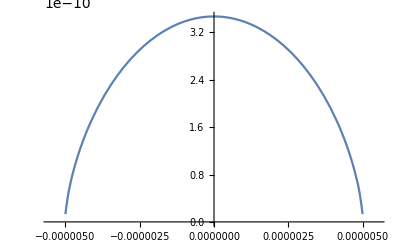

```mathematica
Plot[{Sol2[z]},{z,-1.1*dd/2,1.1*dd/2}]
```

## New exclusion plot

### Derivation cutoff for beta

As mentioned in the paper, there is a maximally allowed value for beta, if beta gets to large the field profile would become complex. Since large beta means small range, we take to very good approximation the value for beta assuming phiB = 0. This value can be computed analytically, which makes the numerics cleaner.

```mathematica
Sn[π/2,1]
```

-1+π/2

```mathematica
Λ = SetPrecision[10^-9,1000];
mpl=SetPrecision[2.435*10^21,1000];
L=SetPrecision[10*10^-6*m2invMeV,1000];
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[1000*2.51*kgm32MeV4,1000];
β=SetPrecision[10^18,1000];
```

```mathematica
EQN[Λ_,β_,L_,ρ_]:=-1+π/2-(L Λ)/(4*√2)(Λ/(√((Λ^5 mpl)/(β ρ))))^(3/2)
βMax[Λ_,β_,L_,ρ_]:=(Λ^3 mpl)/ρ((4*√2)/(L*Λ)(π/2-1))^(4/3); (*For some reason Mathematicas Solve does not find this solution to EQN==0, I double check below that this is the correct max. Value*)
```

```mathematica
Clear[L,β,L,ρ,mpl]
Assuming[{L>0,Λ>0,β>0,ρ>0,mpl>0},FullSimplify[EQN[Λ,βMax[Λ,β,L,ρ],L,ρ]]]
```

0

```mathematica
Assuming[{L>0,Λ>0,β>0,ρ>0,mpl>0},Solve[EQN[Λ,β,L,ρ]==0,β]]
```

{{β→Root[-1024 mpl^3 Λ^5+2048 mpl^3 π Λ^5-1536 mpl^3 π^2 Λ^5+512 mpl^3 π^3 Λ^5-64 mpl^3 π^4 Λ^5+L^4 ρ^3 #1^3&,1]}}

### Pressure and limits

```mathematica
Clear[Sn]
Sn[u_,k_]:=(u-EllipticE[u,k^2])/k^2
(*Sn[u_,k_]:=(u-JacobiEpsilon[u,k])/k*)
(*Sn[u_,k_]:=(u-JacobiEpsilon[u,k^2])/k^2*)

Veff[Λ_,β_,ρ_,ϕ_]:=Λ^5/ϕ+β*ρ/mpl ϕ
ϕρ[Λ_,β_,ρ_]:=√((Λ^5 mpl)/(β ρ))
ϕb[Λ_,β_,ρM_,ρV_,ϕ0_]:= (2*ϕρ[Λ,β,ρM]-ϕρ[Λ,β,ρM]^2/ϕρ[Λ,β,ρV]^2 ϕ0-ϕρ[Λ,β,ρM]^2/ϕ0)/(1-ϕρ[Λ,β,ρM]^2/ϕρ[Λ,β,ρV]^2)
(*EQN[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=Sn[ArcSin[√(ϕb[Λ,β,ρM,ρV,ϕ0]/ϕ0)],ϕ0/ϕρ[Λ,β,ρV]]-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(2*√2)(Λ/ϕ0)^(3/2)*)

βMax[Λ_,β_,L_,ρ_]:=(Λ^3 mpl)/ρ((4*√2)/(L*Λ)(π/2-1))^(4/3); (*If β exceeds this value, the field takes complex values, this is mentioned in the paper*)
EQNKORREKT[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=Sn[ArcSin[√(ϕb[Λ,β,ρM,ρV,ϕ0]/ϕ0)],ϕ0/ϕρ[Λ,β,ρV]]-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(4*√2)(Λ/ϕ0)^(3/2)
(*EQNALT[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(2*√2)(Λ/ϕ0)^(3/2)*)

(*ϕ0C should be the correct value, in the paper a factor of 2 was missing in front of sqrt 2*)
ϕ0[Λ_,β_,ρM_,ρV_,L_]:=Block[{res,startp},
startp=Abs[SetPrecision[ϕρ[Λ,β,ρM],1000]];
res=N[(phi0/.SetPrecision[FindRoot[Re[SetPrecision[EQNKORREKT[SetPrecision[Λ,1000],SetPrecision[β,1000],SetPrecision[ρM,1000],SetPrecision[ρV,1000],SetPrecision[phi0,1000],SetPrecision[L,1000]],5CPrec]],{phi0,startp},AccuracyGoal->5CPrec,PrecisionGoal->5CPrec,WorkingPrecision->5 CPrec],5 CPrec]),5CPrec];
Abs[res]];
```

```mathematica
Λ = SetPrecision[2.24*10^-9,1000];
L=SetPrecision[10*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[1000*2.51*kgm32MeV4,1000];
β=SetPrecision[10^10,1000];

Test1[Λ_,β_]:=(β*ϕρ[Λ,β,ρV])/mpl (*Make sure that coupling terms of higher order to matter can be neglected*)
μm=10^-6*m2invMeV; (*1 μm in MeV*)
mm=10^-3*m2invMeV; (*1 mm in MeV*)

MASS[Λ_,β_,ρ_]:=√2 √(Λ^5/(((mpl Λ^5)/(β ρ))^(3/2)));
RangeV[Λ_,β_,ρ_]:=1/MASS[Λ,β,ρ]

ϕ00=ϕ0[Λ,β,ρM,ρV,L];
Pressure[Λ_,β_,ρM_,ρV_]:=If[Test1[Λ,β]>0.01||RangeV[Λ,β,ρM]>2.5μm||β>βMax[Λ,β,L,ρV],0,(Veff[Λ,β,ρV,√((Λ^5 mpl)/(β ρV))]-Veff[Λ,β,ρV,ϕ0[Λ,β,ρM,ρV,L]])*m2invMeV^2/N2invMeV2](*Note that the Check function sets the pressure to 0 if any error in the FindRoot function occurs*)
```

```mathematica
Clear[Λ,β]
Clear[ρV]
L=SetPrecision[10*10^-6*m2invMeV,1000];
ρV=SetPrecision[500*10^9*2.28*10^-22,1000];
Λ = SetPrecision[2.4*10^-9,1000];
M=SetPrecision[10^-4,100];
β=SetPrecision[M^-1,1000];
β/βMax[Λ,β,L,ρV];
RangeV[Λ,β,ρV]/mm
RangeV[Λ,β,ρM]/(2.5μm);
Test1[Λ,β];
Abs[Pressure[Λ,β,ρM,ρV]]/Abs[PressSen[10*10^-6]]
Abs[(Veff[Λ,β,ρV,√((Λ^5 mpl)/(β ρV))]-Veff[Λ,β,ρV,ϕ0[Λ,β,ρM,ρV,L]])*m2invMeV^2/N2invMeV2]/Abs[PressSen[10*10^-6]]
```

0.736510507821679481422734160477961414923747119555901911134168748429482832428456066993407891793453033404523930461091626395108068977093744457325356121791871182261002785799639744164990998278497127929697434651283246110795199563823035445163976096173566724214393896899784882120878729140331283247429323533973778420821396480591240822780180526742372684366133977870556953967440865081893377242164664440299270092829430344635720320397191790097821895561919133608528793836182366343838002999183949394452518217851173895661717811710414300237173210547724081059986694856293264174597586414034224034336148002333830401950175685875577496465778844078935923584881909139910787180282613781655839591018962261798757879464228565855941336456854486155454209486590148189579293328251960940013210550952587869542537310790932370255710529776675596774305542804479839967389739010632513678819563654581678173980142842316952863126649752871933166569538508502523988071118078872544028505701335379573384813519534866118179184825243296239831274520261

3.19478

3.19478

### Plate distance = 10 micro meters

ContourPlot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (100.).

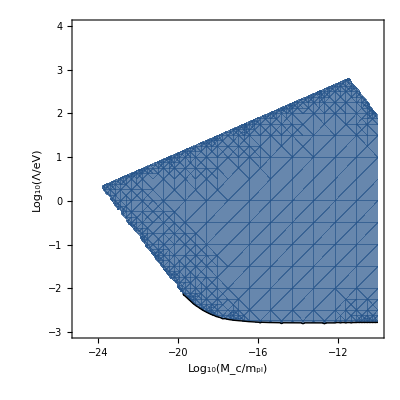

```mathematica
Clear[ρV]
L=SetPrecision[10*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[2514*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
B1=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/Abs[PressSen[10*10^-6]],{β,Log10[10^-25],Log10[10^-10]},{Λ,Log10[10^-3],Log10[10^4]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

```mathematica
Λ=SetPrecision[0.0024,1000];
β=SetPrecision[10^(16),1000];
RangeV[10^-6*Λ,(β),ρM]/μm
```

1.28949622538426408989115521495937113233301329720791832174971100883896647815229557235418604284488493280627751859993653266450639598723415952618484750400774855711925903272031919583773773202786715907010572079313439154068002446061282324557876964929434092365048038723198263343577320188795699239520581489137983454306379264545739439048382703531299075585038606288255257894377720582537314222844250806543039282673628609428364331369233406221802733563990725762949482903855293725625085926094990247010438758987088799044503328816161294244864213275445754454981158250830893105341333393823385502705766136845057145234978301373975326604369690676488286628587232107356439445578411774440544725323038665186810957359424476032189913231082224102024625388004827144754709310342226411126543445688551601534268940803939566925104761331812960064571858103944184645704754613355966086358647547306647969737767928508624386660924084660602603407749194697606778945260594774925859027935020964068605317282905571009533120673974779381344038853107×10^-10

ContourPlot::precw: The precision of the argument function ({«1»,True,True,True,Re[10^(-30+5 Λ)/((10^(-30+β+Times[«2»]))^(3/2))]≤0,Re[10^(-30+β+5 Λ)]≤0,Re[10^(6-Λ)]≤0,Re[10^(-30+5 Λ)/((10^(-30+β+Times[«2»]))^(3/2))]≤0,Re[10^(-30+β+5 Λ)]≤0,Re[10^(6-Λ)]≤0}) is less than WorkingPrecision (100.).

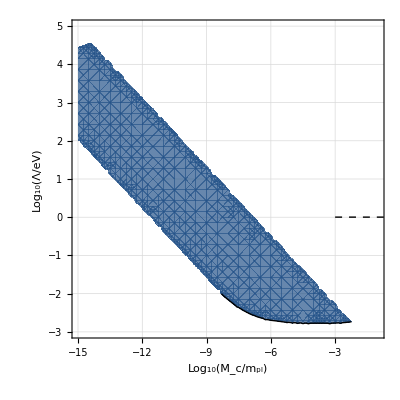

```mathematica
Clear[ρV]
Pressure[Λ_,β_,ρM_,ρV_]:=If[Test1[Λ,β]>0.01||RangeV[Λ,β,ρM]>2.5μm||β>βMax[Λ,β,L,ρV],0,(Veff[Λ,β,ρV,√((Λ^5 mpl)/(β ρV))]-Veff[Λ,β,ρV,ϕ0[Λ,β,ρM,ρV,L]])*m2invMeV^2/N2invMeV2]
L=SetPrecision[10*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[5*10^11*2.28*10^-22,1000];
ρM=SetPrecision[2514*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
B2=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/Abs[PressSen[10*10^-6]],{β,Log10[10^-15],Log10[10^-1]},{Λ,Log10[10^-3],Log10[10^5]},FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)(\!\(\*FractionBox[SubscriptBox[\(M\), \(c\)], SubscriptBox[\(m\), \(pl\)]]\))","\!\(\*SubscriptBox[\(Log\), \(10\)]\)(\!\(\*FractionBox[\(Λ\), \(eV\)]\))"},Contours->{{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None,GridLines->{2.4*10^-3},Epilog->{Dashed,Line[{{Log10[10^-3],2.4*10^-3},{Log10[10^5],2.4*10^-3}}]}]
```

```mathematica
Pressure[Λ_,β_,ρM_,ρV_]:=If[Test1[Λ,β]>0.01||β>βMax[Λ,β,L,ρV],0,(Veff[Λ,β,ρV,√((Λ^5 mpl)/(β ρV))]-Veff[Λ,β,ρV,ϕ0[Λ,β,ρM,ρV,L]])*m2invMeV^2/N2invMeV2]
ρV=SetPrecision[5*10^11*2.28*10^-22,1000];
ρM=SetPrecision[2514*kgm32MeV4,5 CPrec];
β=-1.2;
ϕ0[2.4*10^-6*10^(-3),10^(-β),ρM,ρV,L]
√((Λ^5 mpl)/(10^(-β) ρV))
Abs[Pressure[2.4*10^-6*10^(-3),10^(-β),ρM,ρV]]/Abs[PressSen[10*10^-6]]
```

1.208427379417198668813690183064778975082323024367335478255227201785267970293375068398230690509141885407511970376474296556280149184721591565626930683037180789137135241297917612935001499571364038777507963947028533204192191665662749970978483689750844537324256017957404624566584089322644575923057110003300634414048487913807185125605535014925635119011322602516762924372654577592213037076928397859005634357754857874236715810326101868957707028157681227765713598698646292343506178326393730644401417370836211470635366011974734493874059626955593811341901254571314020583167509648342651590455471909755465894765914213531691349859697112589263362300549792398429589968840121900623387233363887405113925017190851506076332460426256155669283872599334516745832633834897184297328621311802380860728180528737503305242068314342164823504339015594193419779157680895197222315912462662088789264002080266318621855972973222019194358895260935618833225058692096398743643836763383336681108413926131989391178081485176298311220055126268645436811696002301904304000289895546912819518083491530449078808139734041690460444803260074441394569953554293117936912595790437890890034307666036863830887442062582274165798177128454059589565526071600070893675275133452071105937995799319031909417479200108996019923745136524998228948321740089219743234671306586222460843315979974298905775180735986933978998067972069990533240616549559586665587806414867410787366014205309672636992692530985225188217364169882027730645884100193233242464013944177944565540999650900069739738374972987835008136999760910678646036956720353225073709887039301360522937897811864411751885349361408932699258761293469274528728162658414042739534896400629875775245068495816327833048761417740998663750292137020688393808076152689388962546748290067448464436712076674426561599850842078913996744742425930906808792342723820372724777977971616428808528959475591933317426115233163662944610678480686680005249389672505583499200487477092622811281902936331107020292632284398733376307339830742097541222073122474866045608639850161268843536531597826715508767734426311953502016500833330164881848737504462115970735930680159285485723146508613197957894824200689632135619481987577301429174246351549718821501769130188295745716888405790789035523614591114134197754480725963429403499817620537965079507480811745885307389761689804712886199817723542190665925782976221236357952630414959738108135522111247221937665952284088236215248054301545051191729798399582236397292877502575464601055088598008716201661527213924200352×10^-9

3.2761×10^-7

0.991981

```mathematica
β>βMax[Λ,β,L,ρV]
```

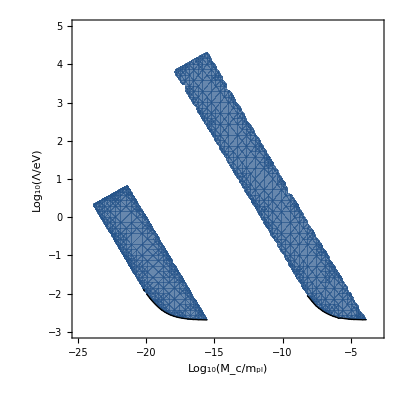

```mathematica
Exclusion2=Show[B1,B2]
```

```mathematica
Export["Exclusion10m.png",Exclusion2,ImageResolution->400];
```

```mathematica
Y
```

RGBColor[0.148, 0.33, 0.54]

### Plate distance = 3 micro meters

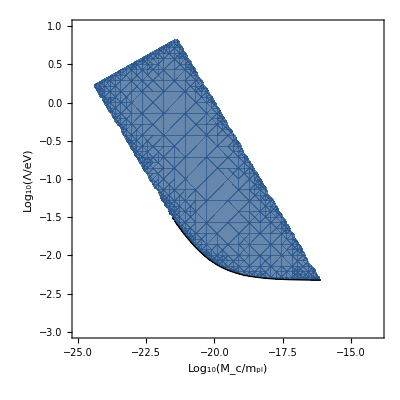

```mathematica
Clear[ρV]
L=SetPrecision[3*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
C1=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[3*10^-6] 1*^12),{β,Log10[10^-25],Log10[10^-14]},{Λ,Log10[10^-3],Log10[10^1]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

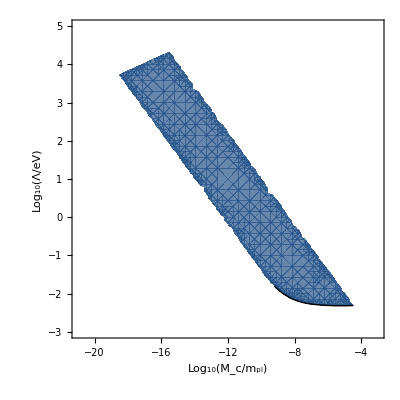

```mathematica
Clear[ρV]
L=SetPrecision[3*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[5*10^11*2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
C2=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[3*10^-6] 1*^12),{β,Log10[10^-21],Log10[10^-3]},{Λ,Log10[10^-3],Log10[10^5]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

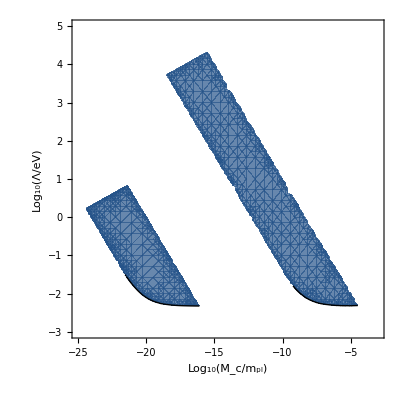

```mathematica
Exclusion3=Show[C1,C2]
```

```mathematica
Export["Exclusion3m.png",Exclusion3,ImageResolution->400];
```

### Plate distance = 15 micro meters

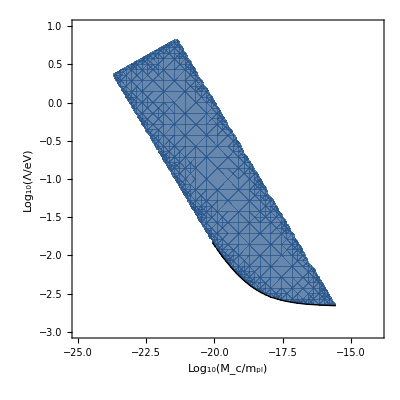

```mathematica
Clear[ρV]
L=SetPrecision[15*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
D1=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[15*10^-6] 1*^12),{β,Log10[10^-25],Log10[10^-14]},{Λ,Log10[10^-3],Log10[10^1]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

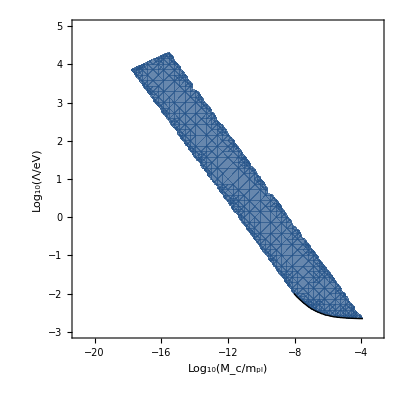

```mathematica
Clear[ρV]
L=SetPrecision[15*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[5*10^11*2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
D2=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[15*10^-6] 1*^12),{β,Log10[10^-21],Log10[10^-3]},{Λ,Log10[10^-3],Log10[10^5]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

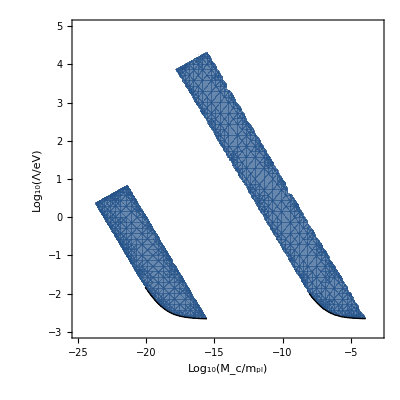

```mathematica
Exclusion4=Show[D1,D2]
```

```mathematica
Export["Exclusion15m.png",Exclusion4,ImageResolution->400];
```

### Plate distance = 30 micro meters

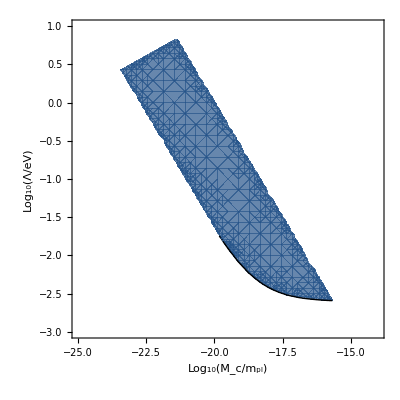

```mathematica
Clear[ρV]
L=SetPrecision[30*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
E1=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[30*10^-6] 1*^12),{β,Log10[10^-25],Log10[10^-14]},{Λ,Log10[10^-3],Log10[10^1]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

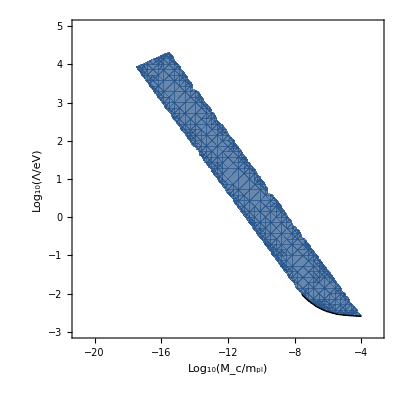

```mathematica
Clear[ρV]
L=SetPrecision[30*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[5*10^11*2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
E2=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[30*10^-6] 1*^12),{β,Log10[10^-21],Log10[10^-3]},{Λ,Log10[10^-3],Log10[10^5]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

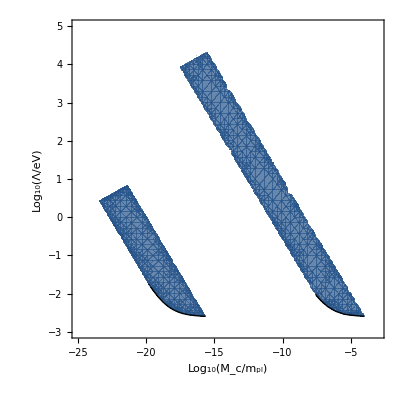

```mathematica
Exclusion5=Show[E1,E2]
```

```mathematica
Export["Exclusion30m.png",Exclusion5,ImageResolution->400];
```

## WRONG exclusion plots I

```mathematica
Clear[Sn]
(*Sn[u_,k_]:=(u-EllipticE[u,k^2])/k^2*)
(*Sn[u_,k_]:=(u-JacobiEpsilon[u,k])/k*)
Sn[u_,k_]:=(u-JacobiEpsilon[u,k^2])/k^2 (*This is how it would follow logically from the paper*)

Veff[Λ_,β_,ρ_,ϕ_]:=Λ^5/ϕ+β*ρ/mpl ϕ
ϕρ[Λ_,β_,ρ_]:=√((Λ^5 mpl)/(β ρ))
ϕb[Λ_,β_,ρM_,ρV_,ϕ0_]:= (2*ϕρ[Λ,β,ρM]-ϕρ[Λ,β,ρM]^2/ϕρ[Λ,β,ρV]^2 ϕ0-ϕρ[Λ,β,ρM]^2/ϕ0)/(1-ϕρ[Λ,β,ρM]^2/ϕρ[Λ,β,ρV]^2)
(*EQN[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=Sn[ArcSin[√(ϕb[Λ,β,ρM,ρV,ϕ0]/ϕ0)],ϕ0/ϕρ[Λ,β,ρV]]-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(2*√2)(Λ/ϕ0)^(3/2)*)

βMax[Λ_,β_,L_,ρ_]:=(Λ^3 mpl)/ρ((4*√2)/(L*Λ)(π/2-1))^(4/3); (*If β exceeds this value, the field takes complex values, this is mentioned in the paper*)
EQNKORREKT[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=Sn[ArcSin[√(ϕb[Λ,β,ρM,ρV,ϕ0]/ϕ0)],ϕ0/ϕρ[Λ,β,ρV]]-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(4*√2)(Λ/ϕ0)^(3/2)
(*EQNALT[Λ_,β_,ρM_,ρV_,ϕ0_,L_]:=-Sn[π/2,ϕ0/ϕρ[Λ,β,ρV]]+(L Λ)/(2*√2)(Λ/ϕ0)^(3/2)*)

(*ϕ0C should be the correct value, in the paper a factor of 2 was missing in front of sqrt 2*)
ϕ0[Λ_,β_,ρM_,ρV_,L_]:=Block[{res,startp},
startp=Abs[SetPrecision[ϕρ[Λ,β,ρM],1000]];
res=N[(phi0/.SetPrecision[FindRoot[Re[SetPrecision[EQNKORREKT[SetPrecision[Λ,1000],SetPrecision[β,1000],SetPrecision[ρM,1000],SetPrecision[ρV,1000],SetPrecision[phi0,1000],SetPrecision[L,1000]],5CPrec]],{phi0,startp},AccuracyGoal->5CPrec,PrecisionGoal->5CPrec,WorkingPrecision->5 CPrec],5 CPrec]),5CPrec];
Abs[res]];
```

```mathematica
Λ = SetPrecision[2.24*10^-9,1000];
L=SetPrecision[10*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[1000*2.51*kgm32MeV4,1000];
β=SetPrecision[10^10,1000];

Test1[Λ_,β_]:=(β*ϕρ[Λ,β,ρV])/mpl (*Make sure that coupling terms of higher order to matter can be neglected*)
μm=10^-6*m2invMeV; (*1 μm in MeV*)
mm=10^-3*m2invMeV; (*1 mm in MeV*)

MASS[Λ_,β_,ρ_]:=√2 √(Λ^5/(((mpl Λ^5)/(β ρ))^(3/2)));
RangeV[Λ_,β_,ρ_]:=1/MASS[Λ,β,ρ]

ϕ00=ϕ0[Λ,β,ρM,ρV,L];
Pressure[Λ_,β_,ρM_,ρV_]:=If[Test1[Λ,β]>0.01||RangeV[Λ,β,ρV]>mm||RangeV[Λ,β,ρM]>2.5μm||β>βMax[Λ,β,L,ρV],0,(Veff[Λ,β,ρV,√((Λ^5 mpl)/(β ρV))]-Veff[Λ,β,ρV,ϕ0[Λ,β,ρM,ρV,L]])*1*^8 m2invMeV^2/N2invMeV2](*Note that the Check function sets the pressure to 0 if any error in the FindRoot function occurs*)
```

```mathematica
Clear[Λ,β]
Clear[ρV]
ρV=SetPrecision[2.28*10^-22,1000];
Λ = SetPrecision[0.5*10^-8,1000];
β=SetPrecision[10^18,1000];
β/βMax[Λ,β,L,ρV];
RangeV[Λ,β,ρV]/mm;
RangeV[Λ,β,ρM]/(2.5μm);
Test1[Λ,β];
Pressure[Λ,β,ρM,ρV]
```

-6.67293376787130779935573721884959208947614666551519907926598764513421153399747602252162458519544526260540555756651777165339758484598926154702962129024870310791766213119130795875036542326850500062887516069016553971456038238511759303816978352473315331108469646094895596007489368149751223382139941245148516113823257902922042192905984215130447242200546036240054110041769253556391676550466946364972093034639768490526276711793034015558840513022959168046550611450727019354121161296566623230329912010390952392579906959855988061716960621375336065908736515436416149268398419905954653662473427536053936283321405575103226549889116295654545996058201403594269182375890753916571159408438088441736846856919168234035714241792847511930302066010704694596719154207129405831868817228152930323009170824167846382054025771664367012905264967153088368493301148365518013890099356062950513141316485913834948150404239300101344001025303299946120541279254871813214586004010110075022198090706002773869415338532500875892835618775105

### Plate distance 10 micro meters

```mathematica
Clear[ρV]
L=SetPrecision[10*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

(*Y=ColorData["M10DefaultDensityGradient"]@0;
B1=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[10*^-6] 1*^12),{β,Log10[10^-25],Log10[10^-14]},{Λ,Log10[10^-3],Log10[10^1]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]*)
```

```mathematica
Clear[press]; 
press={};
nΛ=SetPrecision[100,5CPrec];  (*Compute that many points in the lambda direction*)
nβ=SetPrecision[100,5CPrec]; (*Compute that many points in the A direction*)

Λmin=SetPrecision[-3,5 CPrec]; (*to be read as λmin=10^20 etc*)
Λmax=SetPrecision[1,5 CPrec];
βmin=SetPrecision[-25,5 CPrec];
βmax=SetPrecision[-14,5 CPrec];

ΛIncrement=SetPrecision[(Λmax-Λmin)/nΛ,5CPrec];
βIncrement=SetPrecision[(βmax-βmin)/nβ,5CPrec];

Monitor[For[iβ=1,iβ<=nβ,iβ++,
For[iΛ=1,iΛ<=nΛ,iΛ++,
Block[{A2,λ,At,λt},
βt=βmin+iβ*βIncrement;
Λt=Λmin+iΛ*ΛIncrement;
β=10^β;
Λ=10^Λt;

AppendTo[press,{(βt),Λt,Abs[Pressure[10^-6*10^Λt,10^(-βt),ρM,ρV]]}]]]],iβ]
DumpSave["press.mx",press];
```

```mathematica
press
```

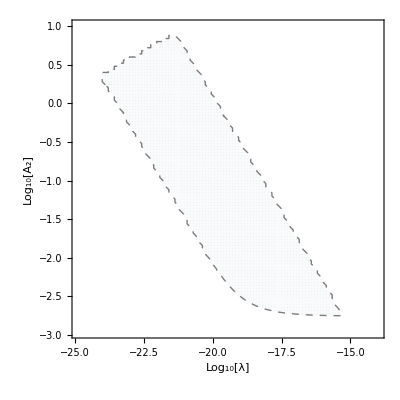

```mathematica
<<press.mx 
Y=ColorData["M10DefaultDensityGradient"]@(0.8*0/27);
A=ListContourPlot[press,Contours->{flimi[10*^-6] 1*^12},FrameLabel->{"Log_10[λ]","Log_10[A_2]"},ContourShading->{Opacity[0.01,White],Opacity[0.01,Y]},PlotRange->All,ContourStyle->Directive[Y,Thick,Black,Dashed]]
```

InterpolatingFunction::dmval: Input value {-24.9992,-2.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

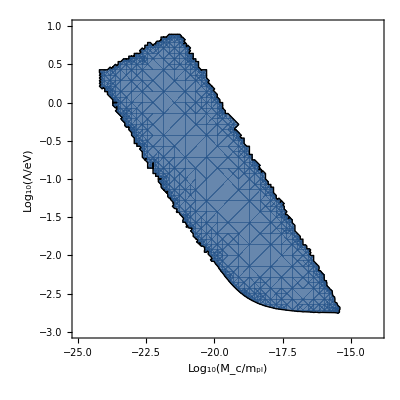

```mathematica
ContourPlot[Abs[f[β,Λ]]/(flimi[10*^-6] 1*^12),{β,Log10[10^-25],Log10[10^-14]},{Λ,Log10[10^-3],Log10[10^1]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

```mathematica
f=Interpolation[press, InterpolationOrder->2];
```

```mathematica
Plot[f[]]
```

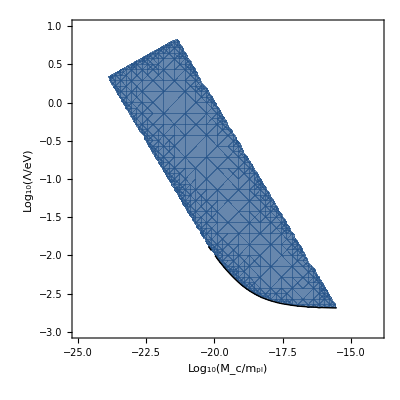

```mathematica
Clear[ρV]
L=SetPrecision[10*10^-6*m2invMeV,1000];
d=L;
ρV=SetPrecision[2.28*10^-22,1000];
ρM=SetPrecision[2700*kgm32MeV4,5 CPrec];

Y=ColorData["M10DefaultDensityGradient"]@0;
B1=ContourPlot[Abs[Pressure[10^-6*10^Λ,10^(-β),ρM,ρV]]/(flimi[10*^-6] 1*^12),{β,Log10[10^-25],Log10[10^-14]},{Λ,Log10[10^-3],Log10[10^1]},FrameLabel->{"Log_10(M_c/m_pl)","Log_10(Λ/eV)"},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.7,Y]},PlotRange->All,WorkingPrecision->100,ContourStyle->Directive[Y,Thick,Black],PlotTheme->None]
```

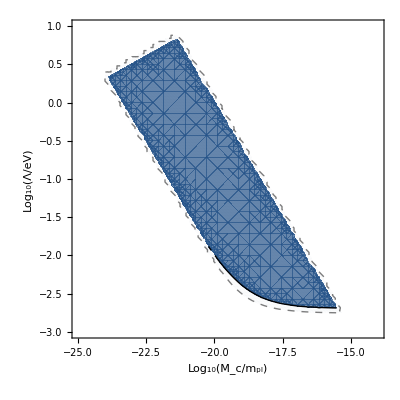

```mathematica
Show[B1,A]
```

## Simulations I: Only two mirror solution

In this section I implement simulations from scratch, for comparison on the one hand, but also to be able to investigate n unequal to 1, as well as to check if the cut-off with 1mm vacuum range makes sense, or if this assumption can be relaxed.

## Define mesh and plate separation etc here

```mathematica
coordlist[dmin_,ddelta_,dfactor_,nmin_,nmax_]:=Block[{i,dummy},
dummy=Table[N[dmin,5 CPrec],nmax-nmin+1];
If[nmin==0,
For[i=1,i<=nmax,i++,
dummy[[i+1]]=dummy[[i]]+N[ddelta*dfactor^i,5 CPrec];
];,
dummy[[1]]+=Sum[N[ddelta*dfactor^i,5 CPrec],{i,1,nmin}];
For[i=2,i<=nmax-nmin+1,i++,
dummy[[i]]=dummy[[i-1]]+N[ddelta*dfactor^(nmin+i-1),5 CPrec];
];];
N[dummy,5 CPrec]
];
Clear[ResIncrease,s,r,z,domb];

Clear[ρV,ρM]

ρV:=2.28274430389522856994287368414079199874719885301117239489836208132800265957484953105449676513671875`1000.*^-20;

rhoV=ρV;

ρM=SetPrecision[2514.0*kgm32MeV4,5 CPrec];

rhoM=ρM;

s=1;

m=m2invMeV;
dd=SetPrecision[10*10^-6,5 CPrec]; (* plate separation *)


Clear[rho];
rho[z_]:=SetPrecision[Piecewise[{{ρV,(-0.5*dd<z<0.5*dd)},{ρM,z≤-0.5*dd||z>=0.5*dd}}],5CPrec];
ρ[z_]:=rho[z]

dist1=SetPrecision[π/(2.0),5CPrec];(* from -∞ to the border of the lower plate*)


(* Was ist dist 2? dp/2 nicht legitim?*)

(*was sollen die kommenden Größen sein?*)
nMaxRes=110*^3;(*max. resolution in the gap 110*^6*)
npts1=80;(*points in free vacuum and free material, 400*)
npts2=80;(*points in the half-gap, 500*)
npts3=80;(*points in the upper plate, 500*)
nFinePoints=30;(*120*)
minMeshSize=SetPrecision[(dd/nMaxRes),5 CPrec];

f1=(*von -π/2 bis -dd/2*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[dist1-dd/2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];
(*f2= (*half thickness of the upper plate*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts3-1}],5 CPrec]==SetPrecision[dist2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];*)
(*f3=(*points above upper plate divided by 2*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[0.5*(dist1-dp-dd/2)-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];*)
f4=(*half gab between plates*)SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts2-1}],5 CPrec]==SetPrecision[dd/2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.001},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];

points=SetPrecision[Sort[N[Join[
(* lower plate *)
coordlist[N[-nFinePoints*minMeshSize-dd/2,5 CPrec],-minMeshSize,f1,1,npts1-1],
Table[N[-i*minMeshSize-dd/2,5 CPrec],{i,0,nFinePoints-1}],
Table[N[i*minMeshSize-dd/2,5 CPrec],{i,1,nFinePoints}],
Table[-π/2+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints}] ,
(*in between plates*)
coordlist[N[nFinePoints*minMeshSize-dd/2,5 CPrec],minMeshSize,f4,1,npts2-2],coordlist[dd/2-N[nFinePoints*minMeshSize,5 CPrec],-minMeshSize,f4,1,npts2-1],
Table[dd/2-N[i*minMeshSize,5 CPrec],{i,0,nFinePoints-1}](* inter-spacing *),
Table[dd/2+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints-1}],

(* upper plate *)
coordlist[N[nFinePoints*minMeshSize+dd/2,5 CPrec],minMeshSize,f1,1,npts1-1],
Table[π/2-N[i*minMeshSize,5 CPrec],{i,1,nFinePoints}]

]]](*free space from right*),5CPrec];
points[[1]]=-π/2;
points[[-1]]=π/(2*s);

domb=SetPrecision[ToElementMesh["Coordinates"->Transpose[{points}],"MeshElements"->{LineElement[Table[{i,i+1},{i,1,Length[points]-1}]]},"BoundaryElements"->{(*external boundaries:*)PointElement[{{1},{Length[points]}}]}],5 CPrec];
Length[points]

Clear[b,A]
b[Λ_,Mc_,n_,rho_,ϕOld_,a_,H_]:= Block[{Output},
Output={};
AppendTo[Output,-n*Λ^(n+4)/ϕOld[[1]]^(n+1)+rho[[1]]/Mc-n*(n+1)Λ^(n+4)/ϕOld[[1]]^(n+2)ϕOld[[1]]+(-a*Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,ρM]])/H[[1]]^2](*From first boundary condition*);
For[i=2, i<=Length[ϕOld]-1,i++, AppendTo[Output, -n*Λ^(n+4)/ϕOld[[i]]^(n+1)+rho[[i]]/Mc-n*(n+1)Λ^(n+4)/ϕOld[[i]]^(n+2)ϕOld[[i]]]];
AppendTo[Output,-n*Λ^(n+4)/ϕOld[[-1]]^(n+1)+rho[[-1]]/Mc-n*(n+1)Λ^(n+4)/ϕOld[[-1]]^(n+2)ϕOld[[-1]]+(-a*Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,ρM]])/H[[-1]]^2](*from 2nd bountady condition*);
Output]
(*Subscript[ρ, i] computes Subscript[ρ, i] prior to the iterations, such that it is not done repeadedly, same for Subscript[h, i]*)
ρi[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points],i++, AppendTo[Output,ρ[points[[i]]]]];
Output]

h[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points]-1,i++, AppendTo[Output,(points[[i+1]]-points[[i]])]];
AppendTo[Output,Output[[-1]]]; (*Subscript[h, N] would point outside the degrees of freedom and is therefore not part of points, I just repeat the last entry*);
Output]

(*H refers to the externally computed h, rho to Subscript[ρ, i]*)
A[Λ_,Mc_,n_,H_,rho_,a_,ϕOld_]:=Block[{Output},
Output=ConstantArray[0,{Length[rho],Length[rho]}](*tridiagonal matrix with mostly 0 elements*); 
Output[[1]][[1]]=-(2a)/H[[1]]^2-n*(n+1)Λ^(n+4)/ϕOld[[1]]^(n+2)(*from boundary*);
Output[[1]][[2]]=a/H[[1]]^2;

For[i=2, i<=Length[H]-1,i++, 
Output[[i]][[i+1]]=(2a)/(H[[i]](H[[i]]+H[[i-1]]));
Output[[i]][[i-1]]=(2a)/(H[[i-1]](H[[i]]+H[[i-1]]));
Output[[i]][[i]]= -(2a)/(H[[i]](H[[i]]+H[[i-1]]))-(2a)/(H[[i-1]](H[[i]]+H[[i-1]]))-n*(n+1)Λ^(n+4)/ϕOld[[i]]^(n+2)(*from boundary*)];
Output[[-1]][[-2]]=(2a)/(H[[-2]](H[[-1]]+H[[-2]]));
Output[[-1]][[-1]]=-(2a)/H[[-1]]^2-n*(n+1)Λ^(n+4)/ϕOld[[-1]]^(n+2)(*from boundary*);
Output

];


(*This function converts the continous function f into a discrete version that can be used as seed for newtons method*)
CreateSeed[f_,points_]:=Block[{Seed},
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,f[points[[i]]]]];
Seed]

TrivialSeed[points_,Λ_,Mc_,n_]:=Block[{Seed},
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,ρM]]]];
Seed]

TrivialSeed2[points_,Λ_,Mc_,n_]:=Block[{Seed,RHO},
RHO=RHO=ρi[points];
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,RHO[[i]]]]]];
Seed]

(*The iterate function takes ϕ^(n-1) and returns ϕ^n*)

Clear[NORM]
NORM[Y1_]:=√Sum[Y1[[i]]^2,{i,Length[points]}]

Iterate[Λ_,Mc_,n_,H_,rho_,a_,ϕOld_]:=Block[{Output,B2,C2},
B2=b[Λ,Mc,n,rho,ϕOld,a,H];
C2=A[Λ,Mc,n,H,rho,a,ϕOld];
Output=LinearSolve[C2,B2];
Output]

(*careful, Seed needs to be converted to a vector prior to using SOLVE*)
SOLVEFD[Λ_,Mc_,n_,a_,points_,Prec_,Max_]:=Block[{YOLD,YNEW,DIFF,M,H,RHO,Func,Output},
M=2;
H=h[points];
RHO=ρi[points];
YOLD=TrivialSeed[points,Λ,Mc,n];
YNEW=Iterate[Λ,Mc,n,H,RHO,a,YOLD];
DIFF=YNEW-YOLD;
While[(NORM[DIFF]/NORM[YOLD]>10^-Prec&&M<=Max),
M=M+1;
YOLD=YNEW;
YNEW=Iterate[Λ,Mc,n,H,RHO,a,YOLD];
DIFF=YNEW-YOLD;
];
Func={};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],YNEW[[i]]}]];
Output=Interpolation[Func,InterpolationOrder->1];
M=M-1;
(*Print["iterations"M]*);
{YNEW,Output}]
```

494

## Simulation

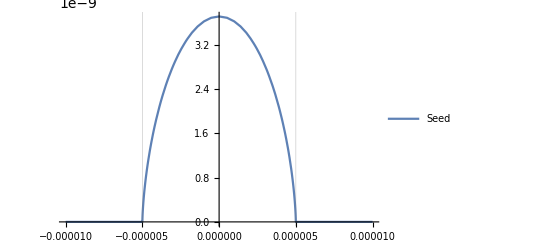

```mathematica
MAX=50;
Prec=15;
n=1;
β=SetPrecision[10^18.1,1000];
Mc=β^-1*mpl;
Λ=10^-8;
a=1/m2invMeV^2;
Sol=SOLVEFD[Λ,Mc,n,a,points,Prec,MAX][[2]];

Plot[{Sol[x]},{x,-dd,dd},GridLines->{{-dd/2,dd/2}},PlotLegends->{"Seed","RealSolution"}]
```

```mathematica
Abs[Pressure[2.4*10^-6*10^(-3),10^(-β),ρM,ρV]]/Abs[PressSen[10*10^-6]]
```

General::munfl: 7.96262×10^-44 1.32083943841298×10^-14975 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

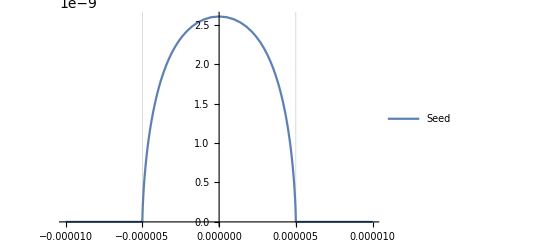

```mathematica
Plot[{Sol[x],ϕ[x*m2invMeV,Λ,β,L,ϕ00C]},{x,-dd,dd},GridLines->{{-dd/2,dd/2}},PlotLegends->{"Seed","RealSolution"}]
```

```mathematica
Sol[x]
```

## Simulations II: Including finite upper mirror for HIGHEST pressure

## Define mesh and plate separation etc here

```mathematica
coordlist[dmin_,ddelta_,dfactor_,nmin_,nmax_]:=Block[{i,dummy},
dummy=Table[N[dmin,5 CPrec],nmax-nmin+1];
If[nmin==0,
For[i=1,i<=nmax,i++,
dummy[[i+1]]=dummy[[i]]+N[ddelta*dfactor^i,5 CPrec];
];,
dummy[[1]]+=Sum[N[ddelta*dfactor^i,5 CPrec],{i,1,nmin}];
For[i=2,i<=nmax-nmin+1,i++,
dummy[[i]]=dummy[[i-1]]+N[ddelta*dfactor^(nmin+i-1),5 CPrec];
];];
N[dummy,5 CPrec]
];
Clear[ResIncrease,s,r,z,domb];

Clear[ρV,ρM]

ρV=SetPrecision[5*10^11*2.28*10^-22,1000];

rhoV=ρV;

ρM=SetPrecision[2514.0*kgm32MeV4,5 CPrec];

rhoM=ρM;

s=1;

m=m2invMeV;
dd=SetPrecision[10*10^-6,5 CPrec]; (* plate separation *)
dp=SetPrecision[100.0*^-6,5CPrec];


Clear[rho];
rho[z_]:=SetPrecision[Piecewise[{{ρV,(-0.5*dd<z<0.5*dd)||z>dd/2+dp}},ρM],5CPrec];
ρ[z_]:=rho[z]

dist1=SetPrecision[0.01,5CPrec];(* from -∞ to the border of the lower plate*)
dd=SetPrecision[10.0*^-6,5 CPrec]; (* plate separation *)
dist2=SetPrecision[dp/2.,5CPrec];

(* Was ist dist 2? dp/2 nicht legitim?*)

(*was sollen die kommenden Größen sein?*)
nMaxRes=200;(*max. resolution in the gap 110*^6*)
npts1=200;(*points in free vacuum and free material, 400*)
npts2=200;(*points in the half-gap, 500*)
npts3=200;(*points in the upper plate, 500*)
nFinePoints=0;(*120*)
minMeshSize=SetPrecision[(dd/nMaxRes),5 CPrec];

f1=SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[dist1-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];
f2=SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts3-1}],5 CPrec]==SetPrecision[dist2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];
f3=SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts1-1}],5 CPrec]==SetPrecision[dist1-dd-dp-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.01},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];
f4=SetPrecision[(δ/.Flatten[FindRoot[SetPrecision[Sum[N[minMeshSize,5 CPrec]*δ^N[n,5 CPrec],{n,1,npts2-1}],5 CPrec]==SetPrecision[dd/2-N[nFinePoints*minMeshSize,5 CPrec],5 CPrec],{δ,1.001},MaxIterations->3000,PrecisionGoal->5 CPrec+2,AccuracyGoal->5 CPrec+2,WorkingPrecision->5 CPrec]][[1]]),5CPrec];
Block[{$MinPrecision=5},Print[N[f1,8],", ",N[f2,8],", ",N[f3,8],", ",N[f4,8]]];

points=SetPrecision[Sort[N[Join[
coordlist[N[-nFinePoints*minMeshSize-dd/2,5 CPrec],-minMeshSize,f1,0,npts1-1],Table[N[-i*minMeshSize-dd/2,5 CPrec],{i,0,nFinePoints-1}](* lower plate *),Table[N[i*minMeshSize-dd/2,5 CPrec],{i,1,nFinePoints}],coordlist[N[nFinePoints*minMeshSize-dd/2,5 CPrec],minMeshSize,f4,1,npts2-2],coordlist[dd/2-N[nFinePoints*minMeshSize,5 CPrec],-minMeshSize,f4,1,npts2-1],Table[dd/2-N[i*minMeshSize,5 CPrec],{i,0,nFinePoints-1}](* inter-spacing *),Table[dd/2+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints-1}],coordlist[dd/2+N[nFinePoints*minMeshSize,5 CPrec],minMeshSize,f2,0,npts3-1](* upper plate 1*),Table[dd/2+dp-N[i*minMeshSize,5 CPrec],{i,0,nFinePoints-1}],coordlist[dd/2+dp-N[nFinePoints*minMeshSize,5 CPrec],-minMeshSize,f2,0,npts3-2](*upper plate,2*),Table[dd/2+dp+N[i*minMeshSize,5 CPrec],{i,1,nFinePoints}],coordlist[dd/2+dp+N[nFinePoints*minMeshSize,5 CPrec],minMeshSize,f3,1,npts1-1]]]](*free space*),5CPrec];
points[[1]]=-dist1;
points[[-1]]=dist1;

points=DeleteDuplicates[points];

domb=SetPrecision[ToElementMesh["Coordinates"->Transpose[{points}],"MeshElements"->{LineElement[Table[{i,i+1},{i,1,Length[points]-1}]]},"BoundaryElements"->{(*external boundaries:*)PointElement[{{1},{Length[points]}}]}],5 CPrec];
Length[points]

Clear[b,A]
b[Λ_,Mc_,n_,rho_,ϕOld_,a_,H_]:= Block[{Output},
Output={};
AppendTo[Output,-n*Λ^(n+4)/ϕOld[[1]]^(n+1)+rho[[1]]/Mc-n*(n+1)Λ^(n+4)/ϕOld[[1]]^(n+2)ϕOld[[1]]+(-a*Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,ρM]])/H[[1]]^2](*From first boundary condition*);
For[i=2, i<=Length[ϕOld]-1,i++, AppendTo[Output, -n*Λ^(n+4)/ϕOld[[i]]^(n+1)+rho[[i]]/Mc-n*(n+1)Λ^(n+4)/ϕOld[[i]]^(n+2)ϕOld[[i]]]];
AppendTo[Output,-n*Λ^(n+4)/ϕOld[[-1]]^(n+1)+rho[[-1]]/Mc-n*(n+1)Λ^(n+4)/ϕOld[[-1]]^(n+2)ϕOld[[-1]]+(-a*Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,ρV]])/H[[-1]]^2](*from 2nd bountady condition*);
Output]
(*Subscript[ρ, i] computes Subscript[ρ, i] prior to the iterations, such that it is not done repeadedly, same for Subscript[h, i]*)
ρi[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points],i++, AppendTo[Output,ρ[points[[i]]]]];
Output]

h[points_]:=Block[{Output},
Output={};
For[i=1, i<=Length[points]-1,i++, AppendTo[Output,(points[[i+1]]-points[[i]])]];
AppendTo[Output,Output[[-1]]]; (*Subscript[h, N] would point outside the degrees of freedom and is therefore not part of points, I just repeat the last entry*);
Output]

(*H refers to the externally computed h, rho to Subscript[ρ, i]*)
A[Λ_,Mc_,n_,H_,rho_,a_,ϕOld_]:=Block[{Output},
Output=ConstantArray[0,{Length[rho],Length[rho]}](*tridiagonal matrix with mostly 0 elements*); 
Output[[1]][[1]]=-(2a)/H[[1]]^2-n*(n+1)Λ^(n+4)/ϕOld[[1]]^(n+2)(*from boundary*);
Output[[1]][[2]]=a/H[[1]]^2;

For[i=2, i<=Length[H]-1,i++, 
Output[[i]][[i+1]]=(2a)/(H[[i]](H[[i]]+H[[i-1]]));
Output[[i]][[i-1]]=(2a)/(H[[i-1]](H[[i]]+H[[i-1]]));
Output[[i]][[i]]= -(2a)/(H[[i]](H[[i]]+H[[i-1]]))-(2a)/(H[[i-1]](H[[i]]+H[[i-1]]))-n*(n+1)Λ^(n+4)/ϕOld[[i]]^(n+2)(*from boundary*)];
Output[[-1]][[-2]]=(2a)/(H[[-2]](H[[-1]]+H[[-2]]));
Output[[-1]][[-1]]=-(2a)/H[[-1]]^2-n*(n+1)Λ^(n+4)/ϕOld[[-1]]^(n+2)(*from boundary*);
Output

];


(*This function converts the continous function f into a discrete version that can be used as seed for newtons method*)
CreateSeed[f_,points_]:=Block[{Seed},
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,f[points[[i]]]]];
Seed]

TrivialSeed[points_,Λ_,Mc_,n_]:=Block[{Seed},
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,ρM]]]];
Seed]

TrivialSeed2[points_,Λ_,Mc_,n_]:=Block[{Seed,RHO},
RHO=RHO=ρi[points];
Seed={};
For[i=1, i<=Length[points],i++, AppendTo[Seed,Block[{$MaxExtraPrecision=1000},ϕρ[Λ,Mc,n,RHO[[i]]]]]];
Seed]

(*The iterate function takes ϕ^(n-1) and returns ϕ^n*)

Clear[NORM]
NORM[Y1_]:=√Sum[Y1[[i]]^2,{i,Length[points]}]

Iterate[Λ_,Mc_,n_,H_,rho_,a_,ϕOld_]:=Block[{Output,B2,C2},
B2=b[Λ,Mc,n,rho,ϕOld,a,H];
C2=A[Λ,Mc,n,H,rho,a,ϕOld];
Output=LinearSolve[C2,B2];
Output]

(*careful, Seed needs to be converted to a vector prior to using SOLVE*)
SOLVEFD[Λ_,Mc_,n_,a_,points_,Prec_,Max_]:=Block[{YOLD,YNEW,DIFF,M,H,RHO,Func,Output},
M=2;
H=h[points];
RHO=ρi[points];
YOLD=TrivialSeed2[points,Λ,Mc,n];
YNEW=Iterate[Λ,Mc,n,H,RHO,a,YOLD];
DIFF=YNEW-YOLD;
While[(NORM[DIFF]/NORM[YOLD]>10^-Prec&&M<=Max),
M=M+1;
YOLD=YNEW;
YNEW=Iterate[Λ,Mc,n,H,RHO,a,YOLD];
DIFF=YNEW-YOLD;
];
Func={};
For[i=1,i<=Length[points],i++,
AppendTo[Func,{points[[i]],YNEW[[i]]}]];
Output=Interpolation[Func,InterpolationOrder->1];
M=M-1;
(*Print["iterations"M]*);
{YNEW,Output}]
```

1.0467808, 1.0134465, 1.0467156, 0.99214344

1195

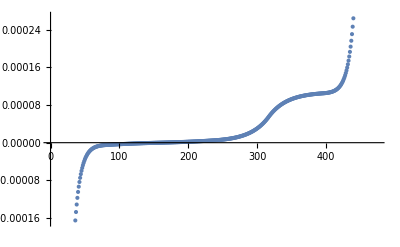

```mathematica
ListPlot[points]
```

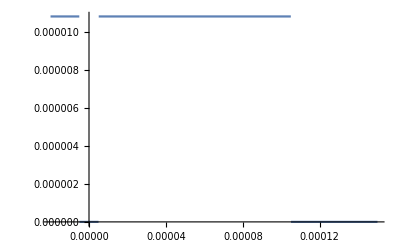

```mathematica
Plot[ρ[z],{z,-20*10^-6,150*10^-6}]
```

```mathematica
MAX=50;
Prec=30;
n=1;
Mc=SetPrecision[10^-16*mpl,1000];
Λ=SetPrecision[10^-8,1000];
a=1/m2invMeV^2;
Sol=SOLVEFD[Λ,Mc,n,a,points,Prec,MAX][[2]];
```

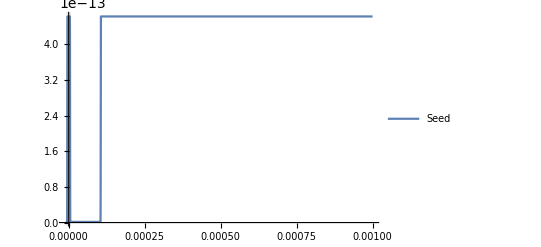

```mathematica
Plot[{Sol[x]},{x,-dd,0.001},GridLines->{{-dd/2,dd/2}},PlotLegends->{"Seed","RealSolution"}]
```

General::munfl: (-2.394528244863451085870576384012470316062085177094545113164345045620821728675222371469825639720076124071937063337913559386036779986552969390825318705106775163858292199685042587695377606287854917544033183653958953007829186035911907072320816642574278930325349981941145099470721904031962215076916105120105688526732923304597630558638878485953594718326315851572247376366407159700512575227308407221938824514531996893293251×10^-584)/(-9.36619×10^-7) is too small to represent as a normalized machine number; precision may be lost.

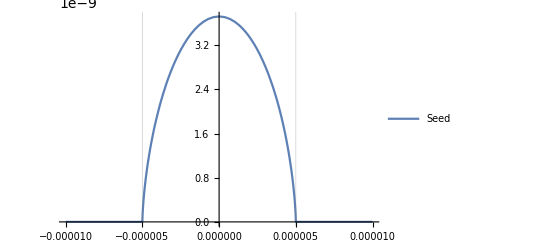

```mathematica
Plot[{Sol[x]},{x,-dd,dd},GridLines->{{-dd/2,dd/2}},PlotLegends->{"Seed","RealSolution"}]
```

## Simulation

1.01740514573815147038365348615788623807172351554667837875070937351285745258239316655794195268217283852849343473091995638856458110261910482979255799323445813508797923991569833725372774447908255829156104978595278783438890844938749090138974628709166795768120115723376892953811900130964451847803576758267920398107037248684203391769570683787758255085907174338776947315100298963401678066019509733762587451477479133171766369878177129428568515139930408883388876169519145187327025948400746649284108916816189609602151010773280120027330888243930891961813603624123695054348219951215145082500168520009548221553878152764019343872546304697458406961590242169294890327603968695502989699248705486592437590221550446979187758048164440144522417936944626767347825178137231187548439848056176544886203936530964334003846376931466539452737612353917521890917586890845914937468685624577348863908901108508572340284438986652601490117212806076859594532112997458894321207814305541213447601088051434935192565873600631909897793229767

Excluded if > 1:

3.20028

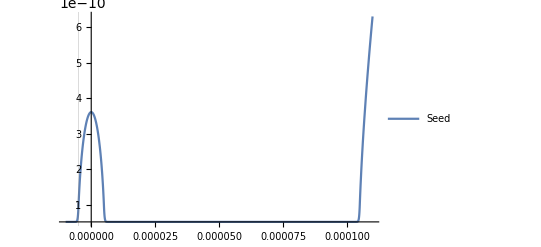

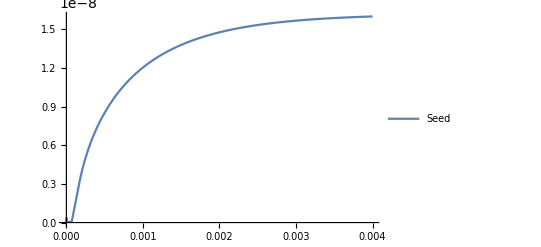

```mathematica
MAX=50;

Prec=15;
n=1;
β=SetPrecision[6.5*10^3,100];
Mc=mpl/β;
Λ=SetPrecision[2.4*10^-6*10^(-3),1000];
1/(μ[Λ,n,Mc,ρV]*mm)
ϕρ[Λ,Mc,n,ρV];


a=1/m2invMeV^2;
Sol=SOLVEFD[Λ,Mc,n,a,points,Prec,MAX][[2]];

Print["Excluded if > 1:"]
Abs[(Veff[Λ,Mc,n,ρV,ϕρ[Λ,Mc,n,ρV]]-Veff[Λ,Mc,n,ρV,SetPrecision[Sol[0],100]])/Abs[PressSen[10*10^-6]]*m2invMeV^2/N2invMeV2]

Plot[{Abs[Sol[x]]},{x,-dd,110*10^-6},GridLines->{{-dd/2,0.1}},PlotLegends->{"Seed","RealSolution"},PlotRange->Full]
Plot[{Abs[Sol[x]]},{x,-dd,4*10^-3},GridLines->{{-dd/2,0.1}},PlotLegends->{"Seed","RealSolution"},PlotRange->Full]
```

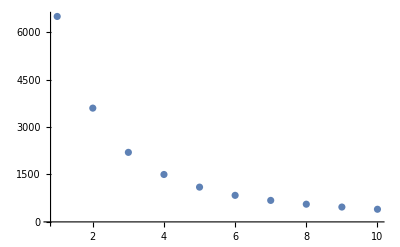

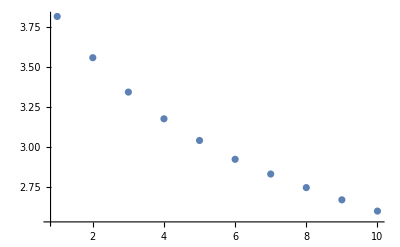

```mathematica
FinalExclusionLine={{1,6.5*10^3},{2,3.6*10^3},{3,2.2*10^3},{4,1.5*10^3},{5,1.1*10^3},{6,8.4*10^2},{7,6.8*10^2},{8,5.6*10^2},{9,4.7*10^2},{10,4*10^2}};
FinalLogExclusionLine={{1,Log10[6.5*10^3]},{2,Log10[3.6*10^3]},{3,Log10[2.2*10^3]},{4,Log10[1.5*10^3]},{5,Log10[1.1*10^3]},{6,Log10[8.4*10^2]},{7,Log10[6.8*10^2]},{8,Log10[5.6*10^2]},{9,Log10[4.7*10^2]},{10,Log10[4*10^2]}};
ListPlot[FinalExclusionLine,PlotRange->Full]
ListPlot[FinalLogExclusionLine,PlotRange->Full]
```

```mathematica
(*NOTE: The above calulation shows that the cannex contour is entirely given by the vacuum range cut-off of 1 mm, hence that is what I use to create a smooth exclusion plot*)
```

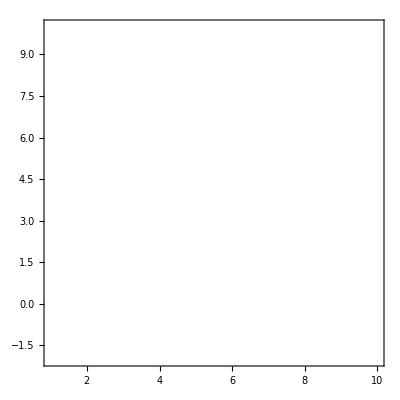

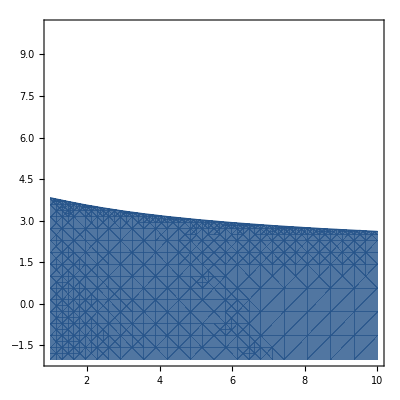

```mathematica
Y=ColorData["M10DefaultDensityGradient"]@0;
BACKGROUND=ContourPlot[0,{n,1,10},{β,Log10[10^-2],Log10[10^10]},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.8,Y]},PlotRange->All,ContourStyle->Directive[Y],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"n","\\log_{10}[\\beta]"}),Exclusions->None,WorkingPrecision->200]
EXCLUSION=ContourPlot[1/(μ[Λ,n,mpl/10^β,ρV]*mm),{n,1,10},{β,Log10[10^-2],Log10[10^10]},Contours-> {{1}},ContourShading->{Opacity[0.01,White],Opacity[0.8,Y]},PlotRange->All,ContourStyle->Directive[Y],PlotTheme->None,LabelStyle->{FontFamily->"Arial", FontSize->13},FrameLabel->(MaTeX[#,Magnification->1.2]&/@{"n","\\log_{10}[\\beta]"}),Exclusions->None,WorkingPrecision->200]
```

```mathematica
Export["BACKGROUND.pdf",BACKGROUND]
Export["EXCLUSION.pdf",EXCLUSION]
```

BACKGROUND.pdf

EXCLUSION.pdf

## 2 Body problem approach